```mathematica
ClearAll[fourierSeriesGraphics]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
With[{protoList=MapThread[{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}]},
Plus@@@Table[protoList[[;;n]],
{n,1,Length[protoList]}]//Prepend[{0,0}]]

fourierSeriesGraphics[numberCircles_,radiusList_List,frequencyList_List]:=With[{coordinateList=Partition[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],2,1],protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],circleList=Apply[,]},
Print[coordinateList];

Animate[
Graphics[
{#1,#2}],{time,0,2*Pi},AnimationRunning->False]&@Evaluate[(Line[#1]&/@coordinateList),(Circle[#1]&/@protoList)]
]
```

```mathematica
ClearAll[fourierSeriesGraphicsV2]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{protoList=MapThread[
						{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}
					]
				},
		Plus@@@Table[protoList[[;;n]],
		{n,1,Length[protoList]}]//Prepend[{0,0}]
]

fourierSeriesGraphicsV2[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{
			coordinateList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			circleList=Evaluate[
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],-1],
							radiusList}
						]
					]
		},
	Print[coordinateList];

	Animate[
		Graphics[{#1,#2}],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
]
```

```mathematica
fourierSeriesCoordinates[50,Reverse[Range[50]],Range[50]]
```

{{0,0},1,47,{1,1},{50 Cos[time]+49 Cos[2 time]+48 Cos[3 time]+47 Cos[4 time]+46 Cos[5 time]+45 Cos[6 time]+44 Cos[7 time]+43 Cos[8 time]+42 Cos[9 time]+41 Cos[10 time]+40 Cos[11 time]+39 Cos[12 time]+26+12 Cos[39 time]+11 Cos[40 time]+10 Cos[41 time]+9 Cos[42 time]+8 Cos[43 time]+7 Cos[44 time]+6 Cos[45 time]+5 Cos[46 time]+4 Cos[47 time]+3 Cos[48 time]+2 Cos[49 time]+Cos[50 time],1}}
 |  |  |  |

```mathematica
Drop[Apply[List,MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[10,Reverse[Range[10]],Range[10]],-1],
							Reverse[Range[10]]}
						]//Last],-1][[1,2]]
```

10 Sin[time]+9 Sin[2 time]+8 Sin[3 time]+7 Sin[4 time]+6 Sin[5 time]+5 Sin[6 time]+4 Sin[7 time]+3 Sin[8 time]+2 Sin[9 time]

```mathematica
fourierSeriesGraphicsV2[5,Reverse[Range[5]],Range[5]]
```

{{0,0},{5 Cos[time],5 Sin[time]},{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time]+Cos[5 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]+Sin[5 time]}}

```mathematica
fourierSeriesGraphics[50,Reverse[Range[50]],Range[50]]
```

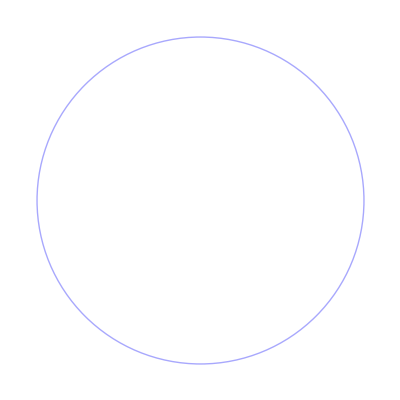

```mathematica
Graphics[Style[Circle[{0,0},5],RandomColor[]]]
```

```mathematica
ClearAll[fourierSeriesGraphicsV2]
fourierSeriesCoordinates[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{protoList=MapThread[
						{#1*Cos[#2*time],#1*Sin[#2*time]}&,{radiusList,frequencyList}
					]
				},
		Plus@@@Table[protoList[[;;n]],
		{n,1,Length[protoList]}]//Prepend[{0,0}]
]

colorList={Table[RGBColor[x,0.3,0.3],{x,0.4,1,0.1}],Table[RGBColor[0.3,x,0.3],{x,0.4,1,0.1}],Table[RGBColor[0.3,0.3,x],{x,0.4,1,0.1}],Table[RGBColor[0.3,x,x],{x,0.4,1,0.1}],Table[RGBColor[x,0.3,x],{x,0.4,1,0.1}],Table[RGBColor[x,x,0.3],{x,0.4,1,0.1}]}

fourierSeriesGraphicsV3[numberCircles_,radiusList_List,frequencyList_List]:=
	With[
		{
			coordinateList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			protoList=fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],
			circleList=Evaluate[
					Style[#1,colorList]&/@
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[numberCircles,radiusList,frequencyList],-1],
							radiusList}
						]
					]
		},

	Animate[
	
		Graphics[{#1,#2}],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
]
```

{{RGBColor[0.4, 0.3, 0.3],RGBColor[0.5, 0.3, 0.3],RGBColor[0.6000000000000001, 0.3, 0.3],RGBColor[0.7000000000000001, 0.3, 0.3],RGBColor[0.8, 0.3, 0.3],RGBColor[0.9, 0.3, 0.3],RGBColor[1., 0.3, 0.3]},{RGBColor[0.3, 0.4, 0.3],RGBColor[0.3, 0.5, 0.3],RGBColor[0.3, 0.6000000000000001, 0.3],RGBColor[0.3, 0.7000000000000001, 0.3],RGBColor[0.3, 0.8, 0.3],RGBColor[0.3, 0.9, 0.3],RGBColor[0.3, 1., 0.3]},{RGBColor[0.3, 0.3, 0.4],RGBColor[0.3, 0.3, 0.5],RGBColor[0.3, 0.3, 0.6000000000000001],RGBColor[0.3, 0.3, 0.7000000000000001],RGBColor[0.3, 0.3, 0.8],RGBColor[0.3, 0.3, 0.9],RGBColor[0.3, 0.3, 1.]},{RGBColor[0.3, 0.4, 0.4],RGBColor[0.3, 0.5, 0.5],RGBColor[0.3, 0.6000000000000001, 0.6000000000000001],RGBColor[0.3, 0.7000000000000001, 0.7000000000000001],RGBColor[0.3, 0.8, 0.8],RGBColor[0.3, 0.9, 0.9],RGBColor[0.3, 1., 1.]},{RGBColor[0.4, 0.3, 0.4],RGBColor[0.5, 0.3, 0.5],RGBColor[0.6000000000000001, 0.3, 0.6000000000000001],RGBColor[0.7000000000000001, 0.3, 0.7000000000000001],RGBColor[0.8, 0.3, 0.8],RGBColor[0.9, 0.3, 0.9],RGBColor[1., 0.3, 1.]},{RGBColor[0.4, 0.4, 0.3],RGBColor[0.5, 0.5, 0.3],RGBColor[0.6000000000000001, 0.6000000000000001, 0.3],RGBColor[0.7000000000000001, 0.7000000000000001, 0.3],RGBColor[0.8, 0.8, 0.3],RGBColor[0.9, 0.9, 0.3],RGBColor[1., 1., 0.3]}}

```mathematica
Table[RGBColor[x,0.3,0.3],{x,0.4,1,0.1}]
```

{RGBColor[0.4, 0.3, 0.3],RGBColor[0.5, 0.3, 0.3],RGBColor[0.6000000000000001, 0.3, 0.3],RGBColor[0.7000000000000001, 0.3, 0.3],RGBColor[0.8, 0.3, 0.3],RGBColor[0.9, 0.3, 0.3],RGBColor[1., 0.3, 0.3]}

```mathematica
Table[RGBColor[0.3,x,0.3],{x,0.4,1,0.1}]
```

{RGBColor[0.3, 0.4, 0.3],RGBColor[0.3, 0.5, 0.3],RGBColor[0.3, 0.6000000000000001, 0.3],RGBColor[0.3, 0.7000000000000001, 0.3],RGBColor[0.3, 0.8, 0.3],RGBColor[0.3, 0.9, 0.3],RGBColor[0.3, 1., 0.3]}

```mathematica
Table[RGBColor[0.3,0.3,x],{x,0.4,1,0.1}]
```

{RGBColor[0.3, 0.3, 0.4],RGBColor[0.3, 0.3, 0.5],RGBColor[0.3, 0.3, 0.6000000000000001],RGBColor[0.3, 0.3, 0.7000000000000001],RGBColor[0.3, 0.3, 0.8],RGBColor[0.3, 0.3, 0.9],RGBColor[0.3, 0.3, 1.]}

```mathematica
colorList={Table[RGBColor[x,0.3,0.3],{x,0.4,1,0.1}],Table[RGBColor[0.3,x,0.3],{x,0.4,1,0.1}],Table[RGBColor[0.3,0.3,x],{x,0.4,1,0.1}]}
```

{{RGBColor[0.4, 0.3, 0.3],RGBColor[0.5, 0.3, 0.3],RGBColor[0.6000000000000001, 0.3, 0.3],RGBColor[0.7000000000000001, 0.3, 0.3],RGBColor[0.8, 0.3, 0.3],RGBColor[0.9, 0.3, 0.3],RGBColor[1., 0.3, 0.3]},{RGBColor[0.3, 0.4, 0.3],RGBColor[0.3, 0.5, 0.3],RGBColor[0.3, 0.6000000000000001, 0.3],RGBColor[0.3, 0.7000000000000001, 0.3],RGBColor[0.3, 0.8, 0.3],RGBColor[0.3, 0.9, 0.3],RGBColor[0.3, 1., 0.3]},{RGBColor[0.3, 0.3, 0.4],RGBColor[0.3, 0.3, 0.5],RGBColor[0.3, 0.3, 0.6000000000000001],RGBColor[0.3, 0.3, 0.7000000000000001],RGBColor[0.3, 0.3, 0.8],RGBColor[0.3, 0.3, 0.9],RGBColor[0.3, 0.3, 1.]}}

```mathematica
fourierSeriesGraphicsV3[5,Reverse[Range[5]],Range[5]]
```

```mathematica
Graphics[Style[{#1,#2},RandomColor[]]],
	{time,0,2*Pi},
	AnimationRunning->False]&@Evaluate[
		(Line[coordinateList]),(circleList)
	]
```

```mathematica
Style[#1,RandomColor]&/@{Circle[{0,0},5],Circle[{0,1},5],Circle[{0,2},5],Circle[{0,3},5]}
```

{Style[Circle[{0,0},5],RandomColor],Style[Circle[{0,1},5],RandomColor],Style[Circle[{0,2},5],RandomColor],Style[Circle[{0,3},5],RandomColor]}

```mathematica
Style[#1,RandomColor]&/@
					MapThread[
						Circle,{
							Drop[fourierSeriesCoordinates[5,Reverse[Range[5]],Range[5]],-1],
							Reverse[Range[5]]}
						]
```

{Style[Circle[{0,0},5],RandomColor],Style[Circle[{5 Cos[time],5 Sin[time]},4],RandomColor],Style[Circle[{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},3],RandomColor],Style[Circle[{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},2],RandomColor],Style[Circle[{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},1],RandomColor]}

```mathematica
Animate[Graphics[{Style[Circle[{0,0},5],RandomColor],Style[Circle[{5 Cos[time],5 Sin[time]},4],RandomColor],Style[Circle[{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},3],RandomColor],Style[Circle[{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},2],RandomColor],Style[Circle[{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time]+2 Cos[4 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]+2 Sin[4 time]},1],RandomColor]}],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[Graphics[{Style[Circle[{5 Cos[time]+4 Cos[2 time],5 Sin[time]+4 Sin[2 time]},3],RandomColor[]],Style[Circle[{5 Cos[time]+4 Cos[2 time]+3 Cos[3 time],5 Sin[time]+4 Sin[2 time]+3 Sin[3 time]},2],RandomColor]}],{time,0,2*Pi},AnimationRunning->False]
```